```mathematica
(*Mathematica*)
```

```mathematica
(* quartic polynomials*)
```

```mathematica
(*2nd minimal Pisot, Meyerhoff,6_1 Knot, tetrahedron, Cyclotomic, Bonacci, M003(-4,3)hyperbolic 3 manifold,8_18 Knot,8_21 Knot,M015(81) hyperbolic manifold,m011 cusped Manifold,m079 cusped manifold,m026 cusped manifold,cyclic,Miniamal Pisot, second cubic pisot, cyclic3,,reverse cyclic3,Weeks Hyperbolic manifold*)
```

```mathematica
p={x^4-x^3-1,x^4-x-1,x^4+x^2-x+1,x^4-2*I*Sqrt[3]*x^2+1,x^4+x^3+x^2+x+1,x^4-x^3-x^2-x-1,x^4-x^3+x^2+x-1,x^4-2*x^3+x^2-2*x+1,x^4-x^3+x+1,x^4-x^2-3*x-2,x^4-2*x^3+x^2-x-1,x^4-x^3+4*x^2-3*x+2,x^4-x^3+x^2-x-1,x^4-1,(x+1)*(x^3-x-1),(x+1)*(x^3-x^2-1),(x+1)(x^3-1),(x-1)*(x^3+1),(x^3-x^2+1)*(x-1)}
```

{-1-x^3+x^4,-1-x+x^4,1-x+x^2+x^4,1-2 ⅈ √3 x^2+x^4,1+x+x^2+x^3+x^4,-1-x-x^2-x^3+x^4,-1+x+x^2-x^3+x^4,1-2 x+x^2-2 x^3+x^4,1+x-x^3+x^4,-2-3 x-x^2+x^4,-1-x+x^2-2 x^3+x^4,2-3 x+4 x^2-x^3+x^4,-1-x+x^2-x^3+x^4,-1+x^4,(1+x) (-1-x+x^3),(1+x) (-1-x^2+x^3),(1+x) (-1+x^3),(-1+x) (1+x^3),(-1+x) (1-x^2+x^3)}

```mathematica
d=Table[Discriminant[p[[i]],x],{i,Length[p]}]
```

{-283,-283,257,4096,125,-563,-331,-448,392,-2151,-751,1929,-563,-256,-23,-279,-108,-108,-23}

```mathematica
(*Polynomials with the same Discriminant*)
```

```mathematica
Delete[Union[Table[If[d[[i]]==d[[j]]&&i ≠ j,{p[[i]],p[[j]]},Nothing],{i,14},{j,i}]],1]
```

{{{-1-x+x^4,-1-x^3+x^4}},{{-1-x+x^2-x^3+x^4,-1-x-x^2-x^3+x^4}}}

```mathematica
(*Gauss sphere projection on unit sphere*)
```

```mathematica
{2*Re[x],2*Im[x],1-Abs[x]^2}/(1+Abs[x]^2)
```

{(2 Re[x])/(1+Abs[x]^2),(2 Im[x])/(1+Abs[x]^2),(1-Abs[x]^2)/(1+Abs[x]^2)}

```mathematica
(*add ones to make tetrahedron Matrices*)
```

```mathematica
pts=Table[{(2 Re[x])/(1+Abs[x]^2),(2 Im[x])/(1+Abs[x]^2),(1-Abs[x]^2)/(1+Abs[x]^2),1}/.NSolve[p[[i]]==0,x],{i,Length[p]}]
```

{{{-0.980432,0.,0.196857,1},{0.232907,-0.970563,0.0613349,1},{0.232907,0.970563,0.0613349,1},{0.950223,0.,-0.311571,1}},{{-0.950223,0.,0.311571,1},{-0.232907,-0.970563,-0.0613349,1},{-0.232907,0.970563,-0.0613349,1},{0.980432,0.,-0.196857,1}},{{-0.428339,-0.877042,-0.217537,1},{-0.428339,0.877042,-0.217537,1},{0.666509,-0.713053,0.217537,1},{0.666509,0.713053,0.217537,1}},{{-0.57735,-0.57735,-0.57735,1},{-0.57735,0.57735,0.57735,1},{0.57735,-0.57735,0.57735,1},{0.57735,0.57735,-0.57735,1}},{{-0.809017,-0.587785,0.,1},{-0.809017,0.587785,0.,1},{0.309017,-0.951057,0.,1},{0.309017,0.951057,0.,1}},{{-0.968311,0.,0.249749,1},{-0.091495,-0.975941,0.197909,1},{-0.091495,0.975941,0.197909,1},{0.817544,0.,-0.575866,1}},{{-0.986632,0.,0.162967,1},{0.426615,-0.859536,-0.281419,1},{0.426615,0.859536,-0.281419,1},{0.920019,0.,0.391875,1}},{{-0.207107,-0.978318,0.,1},{-0.207107,0.978318,0.,1},{0.828427,0.,0.560097,1},{0.828427,0.,-0.560097,1}},{{-0.739539,-0.599371,0.306327,1},{-0.739539,0.599371,0.306327,1},{0.739539,-0.599371,-0.306327,1},{0.739539,0.599371,-0.306327,1}},{{-0.959559,0.,0.281508,1},{-0.427802,-0.883121,-0.192568,1},{-0.427802,0.883121,-0.192568,1},{0.846956,0.,-0.531663,1}},{{-0.784307,0.,0.620373,1},{0.280926,-0.958784,-0.042596,1},{0.280926,0.958784,-0.042596,1},{0.824988,0.,-0.56515,1}},{{0.0255727,-0.844861,-0.534375,1},{0.0255727,0.844861,-0.534375,1},{0.553951,-0.795803,0.244613,1},{0.553951,0.795803,0.244613,1}},{{-0.817544,0.,0.575866,1},{0.091495,-0.975941,-0.197909,1},{0.091495,0.975941,-0.197909,1},{0.968311,0.,-0.249749,1}},{{-1.,0.,0.,1},{0.,-1.,0.,1},{0.,1.,0.,1},{1.,0.,0.,1}},{{-1.,0.,0.,1},{-0.754878,-0.640819,0.139681,1},{-0.754878,0.640819,0.139681,1},{0.961725,0.,-0.274015,1}},{{-1.,0.,0.,1},{-0.276742,-0.942209,0.188829,1},{-0.276742,0.942209,0.188829,1},{0.931142,0.,-0.364656,1}},{{-1.,0.,0.,1},{-0.5,-0.866025,1.11022×10^-16,1},{-0.5,0.866025,1.11022×10^-16,1},{1.,0.,0.,1}},{{-1.,0.,0.,1},{0.5,-0.866025,0.,1},{0.5,0.866025,0.,1},{1.,0.,0.,1}},{{-0.961725,0.,0.274015,1},{0.754878,-0.640819,-0.139681,1},{0.754878,0.640819,-0.139681,1},{1.,0.,0.,1}}}

```mathematica
Table[Eigenvalues[pts[[i]]]//Chop,{i,Length[pts]}]
```

{{-1.42223,1.08343,-0.998888,0.448022},{-1.48903,1.36771,-0.430403+0.391605 ⅈ,-0.430403-0.391605 ⅈ},{1.79386,-1.23422,1.1066,0},{1.53575,-1.26396,0.652782+1.07711 ⅈ,0.652782-1.07711 ⅈ},{1.74196,-1.4748,0.511602,0},{-1.47765,0.812272+0.523302 ⅈ,0.812272-0.523302 ⅈ,-0.893236},{1.68669,-1.37418,-0.720053+0.591502 ⅈ,-0.720053-0.591502 ⅈ},{1.11026+0.86814 ⅈ,1.11026-0.86814 ⅈ,1.12577,-1.01499},{1.61858,-1.49445,0.429378,0},{-1.45246,1.08614,-0.334466+0.602377 ⅈ,-0.334466-0.602377 ⅈ},{-1.28958,0.923419,-0.809373,0.389844},{1.81832,1.10439,-0.807663,0},{1.42953,-1.40113,-0.509896+0.596022 ⅈ,-0.509896-0.596022 ⅈ},{1.41421,-1.41421,-1.,0},{-1.38916,1.19724,-0.690167,0.380946},{-1.45126,-1.00784,0.852864+0.286748 ⅈ,0.852864-0.286748 ⅈ},{1.41421,-1.41421,-0.866025,0},{1.41421,-1.41421,-0.866025,0},{1.52011,-1.38988,-0.436226+0.129121 ⅈ,-0.436226-0.129121 ⅈ}}

```mathematica
Table[CharacteristicPolynomial[pts[[i]],x],{i,Length[pts]}]
```

{0.689584-1.00044 x-1.80178 x^2+0.88966 x^3+x^4,-0.689584-1.71201 x-1.59354 x^2+0.982121 x^3+x^4,-5.0311×10^-16+2.45004 x-1.59472 x^2-1.66624 x^3+x^4,-3.0792+2.10313 x+6.66134×10^-16 x^2-1.57735 x^3+x^4,1.31433 x-2.43236 x^2-0.778768 x^3+x^4,1.23229+0.0693122 x-1.59809 x^2+0.746342 x^3+x^4,-2.01268-3.60927 x-1.89952 x^2+1.12759 x^3+x^4,-2.2697+2.31723 x+1.0897 x^2-2.33131 x^3+x^4,-1.23827×10^-15+1.03862 x-2.36559 x^2-0.553505 x^3+x^4,-0.748913-0.881387 x-0.857802 x^2+1.03525 x^3+x^4,0.375738-0.615116 x-1.35273 x^2+0.785686 x^3+x^4,-4.61794×10^-17+1.6219 x-0.352431 x^2-2.11505 x^3+x^4,-1.23229-2.06007 x-1.41668 x^2+0.991394 x^3+x^4,-2. x-2. x^2+1. x^3+x^4,0.437272-0.564741 x-1.86673 x^2+0.501138 x^3+x^4,1.18416-0.50398 x-1.92232 x^2+0.75338 x^3+x^4,3.84593×10^-16-1.73205 x-2. x^2+0.866025 x^3+x^4,-1.73205 x-2. x^2+0.866025 x^3+x^4,-0.437272-1.87025 x-2.01943 x^2+0.742225 x^3+x^4}

```mathematica
Dimensions[pts]
```

{19,4,4}

```mathematica
(*Determinant Euclidean/Elliptic volumes of Gauss Sphere projected tetrahedrons from quartic Polynomials*)
```

```mathematica
w=Table[Abs[Det[pts[[i]]]/6]//Chop,{i,Length[pts]}]
```

{0.114931,0.114931,0,0.5132,0,0.205382,0.335446,0.378283,0,0.124819,0.062623,0,0.205382,0,0.0728787,0.19736,0,0,0.0728787}

```mathematica
(* Weeks volume*)
vw=0.94270736277692772092;
```

```mathematica
(*hyperbolic reduction factor:13 tetrahedrons in D_6 Week hyperbolic 3 manifold*)
```

```mathematica
Solve[0.07287866940042459*x-vw==0,x]
```

{{x→12.9353}}

```mathematica
rf=x/.Solve[0.07287866940042459*13-vw*x==0,x][[1]]
```

1.005

```mathematica
(* volume of elliptic Weeks Manifold as D_6*)
```

```mathematica
Clear[vwe]
```

```mathematica
Solve[vwe*vw==1,vwe]
```

{{vwe→1.060774572773363818}}

```mathematica
Table[w[[i]]*d[[i]],{i,Length[w]}]//Chop
```

{-32.5254,-32.5254,0,2102.07,0,-115.63,-111.033,-169.471,0,-268.485,-47.0298,0,-115.63,0,-1.67621,-55.0634,0,0,-1.67621}

```mathematica
Table[w[[i]]/d[[i]],{i,Length[w]}]/0.000058028295128009434
```

{-6.99858,-6.99858,0.,2.15917,0.,-6.28656,-17.4644,-14.5512,0.,-1.,-1.43699,0.,-6.28656,0.,-54.605,-12.1903,0.,0.,-54.605}

```mathematica
Expand[(Fit[Sort[w],{1,x,x^2,x^3,x^4},x]/0.000029614877392701216)]
```

1695.1-1638.73 x+388.629 x^2-30.0077 x^3+0.859287 x^4

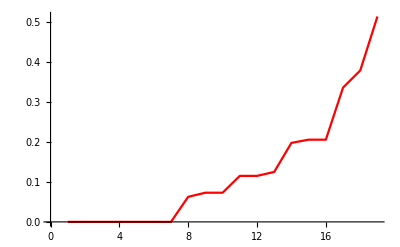

```mathematica
ListLinePlot[Sort[w],PlotStyle->Red]
```

```mathematica
(*Polynomials with singular Determinants: not tetrahedrons*)
```

```mathematica
v=Table[If[w[[i]]==0,p[[i]],Nothing],{i,Length[w]}]
```

{1-x+x^2+x^4,1+x+x^2+x^3+x^4,1+x-x^3+x^4,2-3 x+4 x^2-x^3+x^4,-1+x^4,(1+x) (-1+x^3),(-1+x) (1+x^3)}

```mathematica
Table[Discriminant[v[[i]],x],{i,Length[v]}]
```

{257,125,392,1929,-256,-108,-108}

```mathematica
CompanionMatrix[p_, x_] := Module[{cl=CoefficientList[p, x], deg, m}, cl=Drop[cl/Last[cl], -1]; deg=Length[cl]; If[deg==1, {-cl}, m=RotateLeft[IdentityMatrix[deg]]; m[[ -1]]=-cl; Transpose[m]]];
```

```mathematica
m=Table[Transpose[CompanionMatrix[p[[i]],x]],{i,Length[p]}]
```

{{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,1}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,1,0,0}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1,1,-1,0}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1,0,2 ⅈ √3,0}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1,-1,-1,-1}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,1,1,1}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,-1,-1,1}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1,2,-1,2}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1,-1,0,1}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{2,3,1,0}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,1,-1,2}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-2,3,-4,1}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,1,-1,1}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,0}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,2,1,-1}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,1,1,0}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,1,0,-1}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,-1,0,1}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,-1,-1,2}}}

```mathematica
Table[Max[Abs[N[Eigenvalues[m[[i]]]]]//Chop],{i,Length[p]}]
```

{1.38028,1.22074,1.24741,1.93185,1.,1.92756,1.33539,1.8832,1.3723,1.80843,1.89718,1.8153,1.29065,1.,1.32472,1.46557,1.,1.,1.15096}

```mathematica
(*end*)
```